# BT to PP-STM: some ideas

This notebook contains ideas and test for implementation of BT into PPSTM code.
One of the possible simplification can be usage of Rescaled coefficients, than the full Bloch Theorem (1st part)
The second is to expand these rescaled coefficients (derived later) rather than change the C++ part

```mathematica
F1[k_,c_,x_]:=Cos[k*x]*(Exp[-x^2/(2*c^2)]+Exp[-(x-1)^2/(2*c^2)]+Exp[-(x-2)^2/(2*c^2)]+Exp[-(x-3)^2/(2*c^2)]+Exp[-(x-4)^2/(2*c^2)])
F2[k_,c_,x_]:=(Cos[k*0]*Exp[-x^2/(2*c^2)]+Cos[k*1]*Exp[-(x-1)^2/(2*c^2)]+Cos[k*2]*Exp[-(x-2)^2/(2*c^2)]+Cos[k*3]*Exp[-(x-3)^2/(2*c^2)]+Cos[k*4]*Exp[-(x-4)^2/(2*c^2)])
```

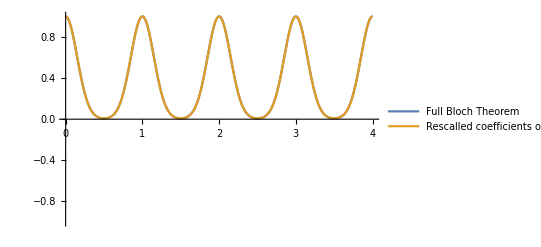

```mathematica
k=0;c=0.15;
Plot[{F1[k,c,x],F2[k,c,x]},{x,0,4},PlotRange->{-1,1},PlotLegends->{"Full Bloch Theorem","Rescalled coefficients only"}]
```

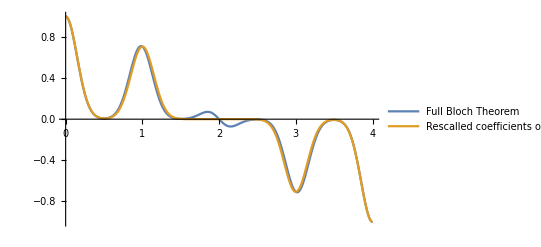

```mathematica
k=Pi/4;c=0.15;
Plot[{F1[k,c,x],F2[k,c,x]},{x,0,4},PlotRange->{-1,1},PlotLegends->{"Full Bloch Theorem","Rescalled coefficients only"}]
```

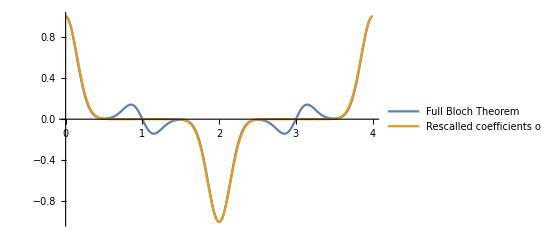

```mathematica
k=Pi/2;c=0.15;
Plot[{F1[k,c,x],F2[k,c,x]},{x,0,4},PlotRange->{-1,1},PlotLegends->{"Full Bloch Theorem","Rescalled coefficients only"}]
```

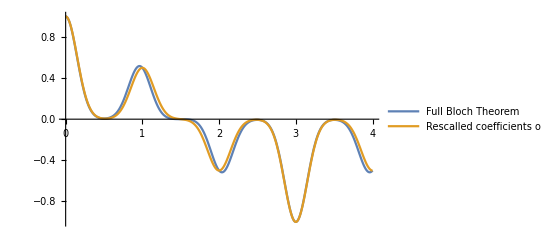

```mathematica
k=Pi/3;c=0.15;
Plot[{F1[k,c,x],F2[k,c,x]},{x,0,4},PlotRange->{-1,1},PlotLegends->{"Full Bloch Theorem","Rescalled coefficients only"}]
```

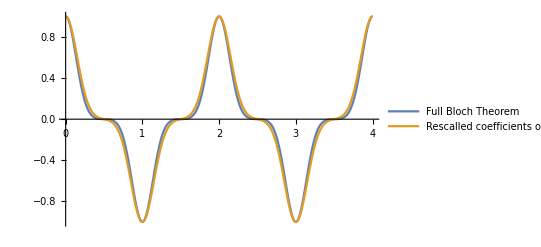

```mathematica
k=Pi;c=0.15;
Plot[{F1[k,c,x],F2[k,c,x]},{x,0,4},PlotRange->{-1,1},PlotLegends->{"Full Bloch Theorem","Rescalled coefficients only"}]
```

Expanding of Rescaled coefficients

```mathematica
(*ReC - Real part of the LCAO coefficient
ImC - Imaginary part of the LCAO coefficient
R - Radial exponential function
Phi - Spherical harmonics
K - rescalling constants
k - k-point
rA - position of nuclei (from 0,0,0) *)
```

```mathematica
(* Function to be expanded*)
R*Phi*(Cos[k*rA]+I Sin[k*rA])(ReC + I ImC)
```

```mathematica
(* Expansion of the function *)
Expand[R*Phi*(Cos[k*rA] + I Sin[k*rA]) (ReC + I ImC)]
```

ⅈ ImC Phi R Cos[k rA]+Phi R ReC Cos[k rA]-ImC Phi R Sin[k rA]+ⅈ Phi R ReC Sin[k rA]

```mathematica
(* Abs ^2 *)
Expand[(Phi R ReC Cos[k rA]-ImC Phi R Sin[k*rA])^2+(Phi R ReC Sin[k*rA]+ImC Phi R Cos[k rA])^2]
```

ImC^2 Phi^2 R^2 Cos[k rA]^2+Phi^2 R^2 ReC^2 Cos[k rA]^2+ImC^2 Phi^2 R^2 Sin[k rA]^2+Phi^2 R^2 ReC^2 Sin[k rA]^2

```mathematica
(Phi*R*ImC*Cos[k rA] )^2+(Phi*R*ReC*Cos[k rA])^2+(Phi*R*ImC*Sin[k rA])^2+(Phi*R*ReC*Sin[k rA])^2
```

ImC^2 Phi^2 R^2 Cos[k rA]^2+Phi^2 R^2 ReC^2 Cos[k rA]^2+ImC^2 Phi^2 R^2 Sin[k rA]^2+Phi^2 R^2 ReC^2 Sin[k rA]^2

```mathematica
Out[9]-Out[10]
```

0

It seems, that at the end, we can try to stick with code without k-points inside the calculating procedure:
During the reading you enlarge the number of coefficients 4 times - you will multiply Real part of the coefficient by Cos [k *rA] then by Sin [k * rA] and then do the same thing with Imaginary part. Just beware in what units you are with the k-points. Therefore you just need to adjust PyPPSTM/ReadSTM.py accordingly.